```mathematica
q={{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}
```

{{0.074195,0.7831},{0.077316,0.7739},{0.144645,0.6322},{0.18457,0.5609},{0.0155,0.7497},{0.01528,0.8906},{0.016587,0.8799},{0.017259,0.8745},{0.040169,0.7353},{0.015218,0.9216},{0.016171,0.9175},{0.017171,0.9159},{0.040309,0.8201},{0.074283,0.6916},{0.07781,0.682},{0.094418,0.6289},{0.074309,0.753},{0.094648,0.6975}}

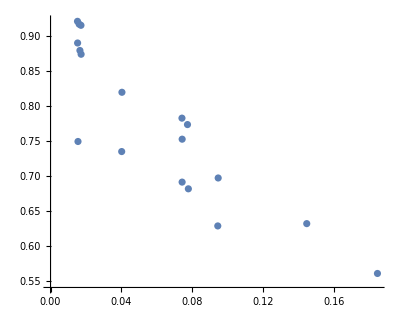

```mathematica
nlm=NonlinearModelFit[q,Exp[a l/(b+c l)],{a,b,c},l];
{bands90[l_],bands95[l_],bands99[l_],bands999[l_]}=Table[nlm["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.9,.95,.99,.999}}];
Show[ListPlot[q],Plot[{nlm[l],bands90[l],bands95[l],bands99[l],bands999[l]},{x,1,15},Filling->{2->{1},3->{2},4->{3},5->{4}}],AspectRatio->4/5]
```

```mathematica
lm=LinearModelFit[q,{1,x},x]
```

FittedModel[0.894171-2.00656 x]

```mathematica
lm["SinglePredictionConfidenceIntervalTable",ConfidenceLevel->0.95]
```

Observed | Predicted | Standard Error | Confidence Interval
0.7831 | 0.745294 | 0.0555981 | {0.627431,0.863156}
0.7739 | 0.739031 | 0.0556595 | {0.621038,0.857024}
0.6322 | 0.603931 | 0.0598884 | {0.476973,0.730889}
0.5609 | 0.523819 | 0.0646877 | {0.386687,0.660951}
0.7497 | 0.863069 | 0.0567782 | {0.742704,0.983433}
0.8906 | 0.86351 | 0.0567907 | {0.743119,0.983901}
0.8799 | 0.860888 | 0.0567168 | {0.740653,0.981122}
0.8745 | 0.859539 | 0.0566796 | {0.739384,0.979695}
0.7353 | 0.813569 | 0.0557461 | {0.695392,0.931745}
0.9216 | 0.863635 | 0.0567943 | {0.743236,0.984033}
0.9175 | 0.861722 | 0.0567401 | {0.741439,0.982006}
0.9159 | 0.859716 | 0.0566845 | {0.73955,0.979881}
0.8201 | 0.813288 | 0.0557424 | {0.695119,0.931457}
0.6916 | 0.745117 | 0.0555996 | {0.627251,0.862983}
0.682 | 0.73804 | 0.0556703 | {0.620024,0.856056}
0.6289 | 0.704715 | 0.0562164 | {0.585541,0.823888}
0.753 | 0.745065 | 0.0556001 | {0.627198,0.862932}
0.6975 | 0.704253 | 0.0562265 | {0.585059,0.823448}

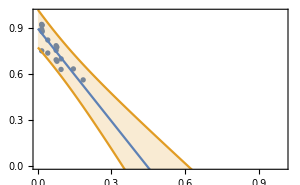

```mathematica
Show[ListPlot[q],Plot[{lm[x],lm["SinglePredictionBands",ConfidenceLevel->0.95]},{x,0,1},Filling->{2->{1}}],PlotRange->{Automatic,{0,1}},Frame->True,ImageSize->300]
```

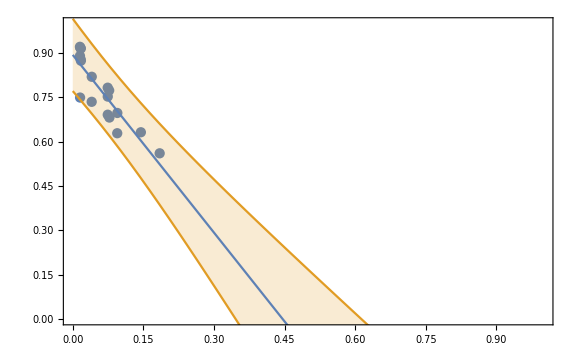

```mathematica
Show[%19,ImageSize->Large]
```

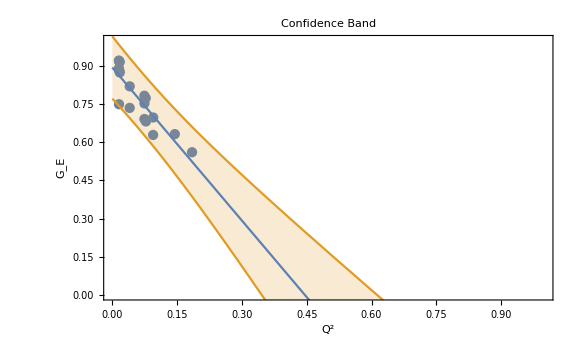

```mathematica
Show[%20,FrameLabel->{{HoldForm[Subscript["G", "E"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Confidence Band],LabelStyle->{12,GrayLevel[0],Bold}]
```

```mathematica
f={{0.074195,2.1849},{0.077316,2.1592},{0.144645,1.764},{0.18457,1.5651},{0.0155,2.0918},{0.01528,2.4848},{0.016587,2.4551},{0.017259,2.4401},{0.040169,2.0515},{0.015218,2.5714},{0.016171,2.56},{0.017171,2.5556},{0.040309,2.288},{0.074283,1.9297},{0.07781,1.9028},{0.094418,1.7547},{0.074309,2.1009},{0.094648,1.9461}}
```

{{0.074195,2.1849},{0.077316,2.1592},{0.144645,1.764},{0.18457,1.5651},{0.0155,2.0918},{0.01528,2.4848},{0.016587,2.4551},{0.017259,2.4401},{0.040169,2.0515},{0.015218,2.5714},{0.016171,2.56},{0.017171,2.5556},{0.040309,2.288},{0.074283,1.9297},{0.07781,1.9028},{0.094418,1.7547},{0.074309,2.1009},{0.094648,1.9461}}

```mathematica
lm1=LinearModelFit[f,{1,x},x]
```

FittedModel[2.49484-5.59839 x]

```mathematica
lm1["SinglePredictionConfidenceIntervalTable",ConfidenceLevel->0.95]
```

Observed | Predicted | Standard Error | Confidence Interval
2.1849 | 2.07947 | 0.155145 | {1.75058,2.40836}
2.1592 | 2.062 | 0.155316 | {1.73274,2.39125}
1.764 | 1.68506 | 0.167117 | {1.33079,2.03933}
1.5651 | 1.46155 | 0.180509 | {1.07888,1.84421}
2.0918 | 2.40807 | 0.158438 | {2.07219,2.74394}
2.4848 | 2.4093 | 0.158473 | {2.07335,2.74525}
2.4551 | 2.40198 | 0.158267 | {2.06647,2.73749}
2.4401 | 2.39822 | 0.158163 | {2.06293,2.73351}
2.0515 | 2.26996 | 0.155558 | {1.94019,2.59973}
2.5714 | 2.40965 | 0.158483 | {2.07368,2.74561}
2.56 | 2.40431 | 0.158332 | {2.06866,2.73996}
2.5556 | 2.39871 | 0.158176 | {2.06339,2.73403}
2.288 | 2.26918 | 0.155548 | {1.93943,2.59892}
1.9297 | 2.07898 | 0.155149 | {1.75007,2.40788}
1.9028 | 2.05923 | 0.155347 | {1.72991,2.38855}
1.7547 | 1.96625 | 0.15687 | {1.6337,2.2988}
2.1009 | 2.07883 | 0.155151 | {1.74993,2.40774}
1.9461 | 1.96497 | 0.156898 | {1.63236,2.29757}

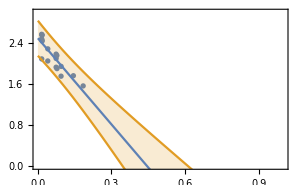

-Graphics-

```mathematica
Show[ListPlot[f],Plot[{lm1[x],lm1["SinglePredictionBands",ConfidenceLevel->0.95]},{x,0,1},Filling->{2->{1}}],PlotRange->{Automatic,{0,3}},Frame->True,ImageSize->300]
```

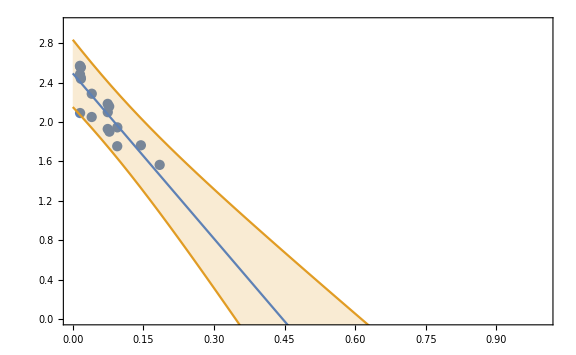

```mathematica
Show[%27,ImageSize->Large]
```

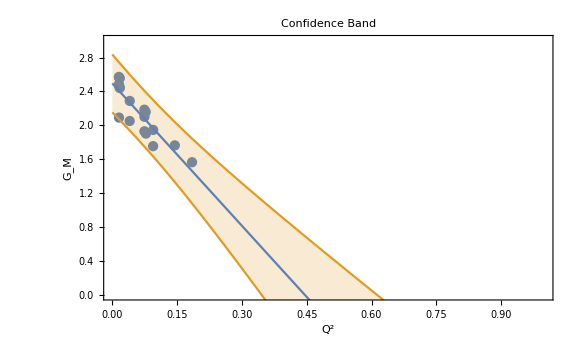

```mathematica
Show[%28,FrameLabel->{{HoldForm[Subscript["G", "M"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Confidence Band],LabelStyle->{12,GrayLevel[0],Bold}]
```

```mathematica
a={{0.074195,0.955349518116384},{0.077316,0.951672405312346},{0.144645,0.916099116070135},{0.18457,0.890458802984601},{0.0155,0.7828129894539},{0.01528,0.929354064489199},{0.016587,0.921554252199413},{0.017259,0.917532263141328},{0.040169,0.820922183766886},{0.015218,0.961602671118531},{0.016171,0.959828433936604},{0.017171,0.960767859016049},{0.040309,0.915903506812598},{0.074283,0.843929225137279},{0.07781,0.83969465648855},{0.094418,0.807317073170732},{0.074309,0.918965096412009},{0.094648,0.895953757225434}}
```

{{0.074195,0.95535},{0.077316,0.951672},{0.144645,0.916099},{0.18457,0.890459},{0.0155,0.782813},{0.01528,0.929354},{0.016587,0.921554},{0.017259,0.917532},{0.040169,0.820922},{0.015218,0.961603},{0.016171,0.959828},{0.017171,0.960768},{0.040309,0.915904},{0.074283,0.843929},{0.07781,0.839695},{0.094418,0.807317},{0.074309,0.918965},{0.094648,0.895954}}

```mathematica
lm2=LinearModelFit[a,{1,x},x]
```

```mathematica
FittedModel[0.9107618762794849-0.18717658463648862 x]
lm2["SinglePredictionConfidenceIntervalTable",ConfidenceLevel->0.95]
```

FittedModel[0.910762-0.187177 x]

Observed | Predicted | Standard Error | Confidence Interval
0.95535 | 0.896874 | 0.0594525 | {0.770841,1.02291}
0.951672 | 0.89629 | 0.0595181 | {0.770117,1.02246}
0.916099 | 0.883688 | 0.0640403 | {0.747928,1.01945}
0.890459 | 0.876215 | 0.0691723 | {0.729576,1.02285}
0.782813 | 0.907861 | 0.0607144 | {0.779152,1.03657}
0.929354 | 0.907902 | 0.0607278 | {0.779165,1.03664}
0.921554 | 0.907657 | 0.0606488 | {0.779087,1.03623}
0.917532 | 0.907531 | 0.060609 | {0.779046,1.03602}
0.820922 | 0.903243 | 0.0596108 | {0.776874,1.02961}
0.961603 | 0.907913 | 0.0607316 | {0.779168,1.03666}
0.959828 | 0.907735 | 0.0606737 | {0.779113,1.03636}
0.960768 | 0.907548 | 0.0606142 | {0.779052,1.03604}
0.915904 | 0.903217 | 0.0596068 | {0.776856,1.02958}
0.843929 | 0.896858 | 0.0594541 | {0.770821,1.02289}
0.839695 | 0.896198 | 0.0595297 | {0.77,1.0224}
0.807317 | 0.893089 | 0.0601137 | {0.765654,1.02052}
0.918965 | 0.896853 | 0.0594546 | {0.770815,1.02289}
0.895954 | 0.893046 | 0.0601244 | {0.765588,1.0205}

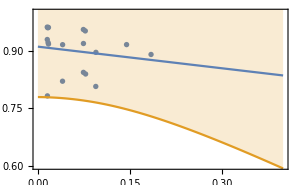
{{-Graphics-},{□}}

```mathematica
{{Show[ListPlot[a],Plot[{lm2[x],lm2["SinglePredictionBands",ConfidenceLevel->0.95]},{x,0,.4},Filling->{2->{1}}],PlotRange->{Automatic,{0.6,1}},Frame->True,ImageSize->300]}, {□}}
```

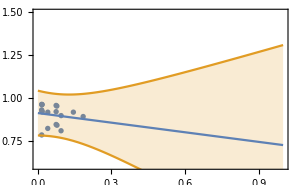

```mathematica
Show[ListPlot[a],Plot[{lm2[x],lm2["SinglePredictionBands",ConfidenceLevel->0.95]},{x,0,1},Filling->{2->{1}}],PlotRange->{Automatic,{0.6,1.5}},Frame->True,ImageSize->300]
```

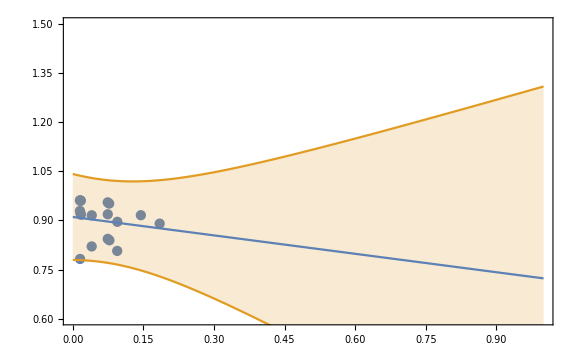

```mathematica
Show[%41,ImageSize->Large]
```

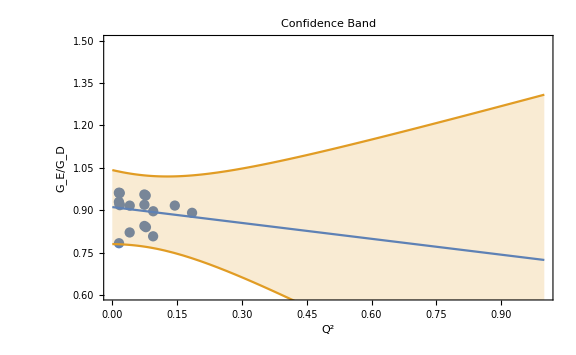

```mathematica
Show[%42,FrameLabel->{{HoldForm[Subscript["G", "E"]/Subscript["G", "D"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Confidence Band],LabelStyle->{12,GrayLevel[0],Bold}]
```